# Diaphorina Model - Pulsos de Paracitoides

## WhenEvent

Agrego WhenEvent a la evolución, el cual añado cada T una cantidad δ de Parasitoides.

```mathematica
ClearAll[SystemEvolve];
SystemEvolve[δ_,T_,{{r1_,b12_,b13_,a1_,c1_},{r2_,b21_,b24_,a2_,c2_},{r3_,b31_,a3_,c3_},{r4_,b42_,a4_,c4_}},{Di0_,B0_,x30_,x40_,tt_}]:=Module[
{x,eqs,x1,x2,x3,x4},
eqs=NDSolve[{
(x1'[t]==x1[t]*(r1+b12*x2[t]+b13*x3[t]-(a1+c1*(b12*x2[t]+b13*x3[t]))*x1[t])), (*Diaphora*)
(x2'[t]==x2[t]*(r2+b21*x1[t]+b24*x4[t]-(a2+c2*(b21*x1[t]+b24*x4[t]))*x2[t])), (*Brotes*)
(x3'[t]==x3[t]*(r3+b31*x1[t]-(a3+c3*b31*x1[t])*x3[t])), (*Parasitoides*)
(x4'[t]==x4[t]*(r4+b42*x2[t]-(a4+c4*b42*x2[t])*x4[t])), (*Brotes*)
x1[0]==Di0,
x2[0]==B0,
x3[0]==x30,
x4[0]==x40,
WhenEvent[Mod[t,T]==0&&t>0,x3[t]->x3[t]+δ]
},
{x1,x2,x3,x4},{t,0,tt},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Plot[Evaluate[{x4[t],x2[t],x1[t],x3[t]}/.eqs],{t,0,tt},PlotLegends->{"Estimulos","Brotes","Parasito (Diaphora)","Parasitoides"},PlotRange->All]]
```

```mathematica
ChartReport[init_,param1_,param2_,param3_,param4_]:=Transpose@Dataset[List@@@Normal[Dataset/@Association[
{"init"->Association@Thread[{"x1[0]","x2[0]","x3[0]","x4[0]","t"}->init]},
{"x1"->Association@Thread[{"r1","b12","b13","a1","c1"}->param1]},{"x2"->Association@Thread[{"r2","b21","b24","a2","c2"}->param2]},{"x3"->Association@Thread[{"r3","b31","a3","c3"}->param3]},{"x4"->Association@Thread[{"r4","b42","a4","c4"}->param4]}]]]
```

### Resultado inicial

Sumar 0 parasitoides recupera el resultado original:

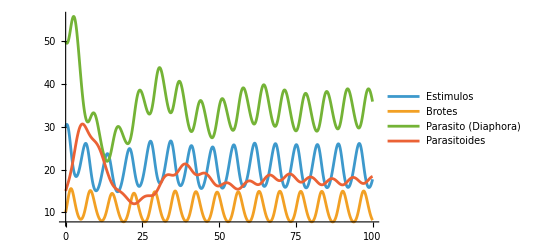

```mathematica
as=0.000555;cs=0.005;
param1={-0.2,0.04,-0.01,as,cs};
param2={-0.72,-0.01,0.054,as,cs};
param3={-0.3,0.01,as,cs};
param4={0.72,-0.072,as,cs};
init={50,10,15,30,100};
ChartReport[init,param1,param2,param3,param4]
SystemEvolve[0,1,{param1,param2,param3,param4},init]
```

### Añadiendo Parasitoides

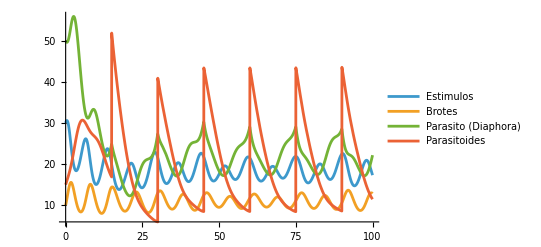

```mathematica
as=0.000555;cs=0.005;
param1={-0.2,0.04,-0.01,as,cs};
param2={-0.72,-0.01,0.054,as,cs};
param3={-0.3,0.01,as,cs};
param4={0.72,-0.072,as,cs};
init={50,10,15,30,100};
ChartReport[init,param1,param2,param3,param4]
SystemEvolve[35,15,{param1,param2,param3,param4},init]
```

Juega con los parámetros:

```mathematica
Manipulate[
SystemEvolve[δ,T,{param1,param2,param3,param4},{50,10,15,30,t}],
{{δ,35},0,100,1},
{{T,15},0,100,1},
{{t,100},1,1000,10}
]
```